## Pre-amble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
```

```mathematica
nCollatz[61]
```

{61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

```mathematica
Select[Map[Rest[#]&,IntegerDigits[Table[k,{k,1001,1100}]]],#[[2]]==4&]
```

{{0,4,0},{0,4,1},{0,4,2},{0,4,3},{0,4,4},{0,4,5},{0,4,6},{0,4,7},{0,4,8},{0,4,9}}

## Topic

### Definition / Theorem

This is text.

#### Example

## Bijection between ℕ and ℚ

### Experiments

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,101,111}]//tf
```

101 | 5/2
102 | -1/51
103 | 1/51
104 | -2/13
105 | 2/13
106 | -1/53
107 | 1/53
108 | -1/18
109 | 1/18
110 | -1/55
111 | 1/55

```mathematica
nQuotientToNatural[5/2]
nQuotientToNatural[-1/53]
nQuotientToNatural[1/55]
```

101

106

111

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,6606600,6606609}]
```

{{6606600,-110/273},{6606601,110/273},{6606602,-1/3303301},{6606603,1/3303301},{6606604,-1/3303302},{6606605,1/3303302},{6606606,-1/3303303},{6606607,1/3303303},{6606608,-1/1651652},{6606609,1/1651652}}

```mathematica
nQuotientToNatural[4/5]
nQuotientToNatural[3/5]
nQuotientToNatural[7/25]
nQuotientToNatural[24/25]
nQuotientToNatural[-44/125]
nQuotientToNatural[117/125]
nQuotientToNatural[-527/625]
nQuotientToNatural[336/625]
nQuotientToNatural[-3116/3125]
nQuotientToNatural[-237/3125]

(4/5+3/5I)^5
```

161

91

12251

144001

12100000

85556251

43395156250

17640000001

37927562500000

219410156250

-3116/3125-(237 ⅈ)/3125

```mathematica
nQuotientToNatural[5/11]
FactorInteger[551]
nIntegerToNatural[19]
```

551

{{19,1},{29,1}}

39

```mathematica
nQuotientToNatural[7/13]
FactorInteger[1275]
nIntegerToNatural[3]
nIntegerToNatural[25]
nIntegerToNatural[17]
```

1275

{{3,1},{5,2},{17,1}}

7

51

35

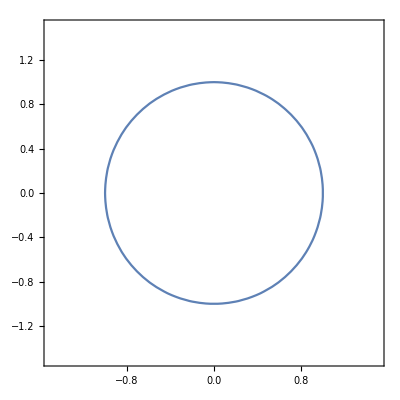

```mathematica
ContourPlot[x^2+y^2==1,{x,-1.5,1.5},{y,-1.5,1.5},AspectRatio->Automatic]
```

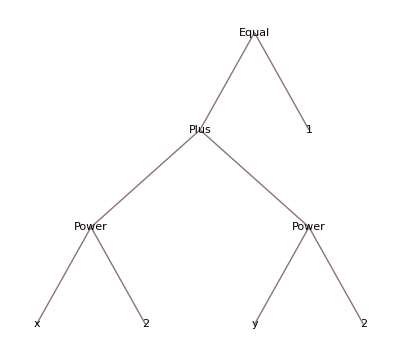

```mathematica
TreeForm[x^2+y^2==1]
```

## COUNTING

## SUMMARY

### Factorial

```mathematica
(* Definition Factorial Function *)
factorial[n_]:=1 /;n==0
factorial[n_]:=Product[k,{k,1,n}] /;n>0
factorial[10]
(* MMa Built-in *)
Factorial[10]
```

3628800

3628800

### Binomial Coefficient

```mathematica
(* Definition Binomial Coefficient *)
binomial[n_,k_]:=factorial[n]/(factorial[k]factorial[n-k])/;n>=0&&k>=0
binomial[6,3]
(* MMa Built-in *)
Binomial[6,3]
```

20

20

### Multinomial Coefficient

```mathematica
(* As used in the Multinomial Theorem *)
g[m_,n_]:=Map[Multinomial[Apply[Sequence,#]]Apply[Times,Apply[Power,{Table[Subscript[x, k],{k,1,m}],#}]]&,Reverse[FrobeniusSolve[ConstantArray[1,m],n]]]
g[3,4]//Total
```

x_1^4+4 x_1^3 x_2+6 x_1^2 x_2^2+4 x_1 x_2^3+x_2^4+4 x_1^3 x_3+12 x_1^2 x_2 x_3+12 x_1 x_2^2 x_3+4 x_2^3 x_3+6 x_1^2 x_3^2+12 x_1 x_2 x_3^2+6 x_2^2 x_3^2+4 x_1 x_3^3+4 x_2 x_3^3+x_3^4

```mathematica
(* MMa Built-in *)
(Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 3])^4//Expand
```

x_1^4+4 x_1^3 x_2+6 x_1^2 x_2^2+4 x_1 x_2^3+x_2^4+4 x_1^3 x_3+12 x_1^2 x_2 x_3+12 x_1 x_2^2 x_3+4 x_2^3 x_3+6 x_1^2 x_3^2+12 x_1 x_2 x_3^2+6 x_2^2 x_3^2+4 x_1 x_3^3+4 x_2 x_3^3+x_3^4

### Anagram Sets

### Types of Braces

### Definitions of Combinatorial Objects

### Words

### Permutations of A

### Partial Permutations

### Anagrams

### Sets

### Multisets

### Functions

### Injections

### Surjections

### Bijections

### Compositions of k

### Lattice Paths

### Dyck Paths

### Basic Counting Rules

### Probability Definitions

## EXERCISES

### 1-5a

```mathematica
5 4 3 2
```

120

```mathematica
Select[Map[Rest[#]&,IntegerDigits[Table[k,{k,10000,19999}]]],
(#[[1]]!=#[[2]]&&
#[[1]]!=#[[3]]&&
#[[1]]!=#[[4]]&&
#[[2]]!=#[[3]]&&
#[[2]]!=#[[4]]&&
#[[3]]!=#[[4]]&&
EvenQ[#[[1]]]&&
EvenQ[#[[2]]]&&
EvenQ[#[[3]]]&&
EvenQ[#[[4]]]
)&]//Length
```

120

### 1-5b

```mathematica
5^5-5!
```

3005

```mathematica
Select[Map[Rest[#]&,IntegerDigits[Table[k,{k,100000,199999}]]],
(Not[
#[[1]]!=#[[2]]&&
#[[1]]!=#[[3]]&&
#[[1]]!=#[[4]]&&
#[[1]]!=#[[5]]&&
#[[2]]!=#[[3]]&&
#[[2]]!=#[[4]]&&
#[[2]]!=#[[5]]&&
#[[3]]!=#[[4]]&&
#[[3]]!=#[[5]]&&
#[[4]]!=#[[5]]]&&
OddQ[#[[1]]]&&
OddQ[#[[2]]]&&
OddQ[#[[3]]]&&
OddQ[#[[4]]]&&
OddQ[#[[5]]]
)&]//Length
```

3005

### 1-6

```mathematica
4 8 8 2
```

512

```mathematica
Select[Map[Rest[#]&,IntegerDigits[Table[k,{k,10000,19999}]]],
(
(OddQ[#[[1]]]&&#[[1]]!=7)&&
(Not[#[[2]]==6||#[[2]]==7])&&
(Not[#[[3]]==6||#[[3]]==7])&&
(#[[4]]==5||#[[4]]==0)
)&]//Length
```

512

### 1-7

```mathematica
7 24
```

168

```mathematica
Select[Map[Rest[#]&,IntegerDigits[Table[k,{k,10000,19999}]]],
(MemberQ[{
{0,1,2,3},{1,2,3,4},{2,3,4,5},{3,4,5,6},{4,5,6,7},{5,6,7,8},{6,7,8,9}},
Sort[{#[[1]],#[[2]],#[[3]],#[[4]]}]
]
)&]//Length
```

168

### 1-8

```mathematica
(9^3-8^3)4
```

868

```mathematica
Select[Map[Rest[#]&,IntegerDigits[Table[k,{k,10000,19999}]]],
(#[[1]]!=2 &&
#[[2]]!=2 &&
#[[3]]!=2 &&
#[[4]]!=2 &&
EvenQ[#[[4]]]&&
(#[[1]]==5||
#[[2]]==5||
#[[3]]==5)
)&]//Length
```

868

### 1-12

```mathematica
testAlphabet:=CharacterRange["A","E"];
alphabet:=CharacterRange["A","Z"];
vowels:={"A","E","I","O","U"};
consonants:={"B","C","D","F","G","H","J","K","L","M","N","P","Q","R","S","T","V","W","X","Y","Z"};
Select[
Map[StringJoin[#]&,Tuples[testAlphabet,2]],
True
&]//Length
```

```mathematica
.b2
```

25

```mathematica
Map[StringJoin[#]&,Select[
Map[#&,Tuples[alphabet,1]],
(MemberQ[vowels,#[[1]]])
&]]//Length

Map[StringJoin[#]&,Select[
Map[#&,Tuples[alphabet,2]],
(MemberQ[vowels,#[[1]]]&&
MemberQ[vowels,#[[2]]]
)
&]]//Length

Map[StringJoin[#]&,Select[
Map[#&,Tuples[alphabet,3]],
(MemberQ[vowels,#[[1]]]&&
MemberQ[vowels,#[[2]]]&&
MemberQ[vowels,#[[3]]]
)
&]]//Length
```

5

25

125

```mathematica
vowels:={"A","E","I","O","U"};
alphabet:=CharacterRange["A","J"];

func[vowels_List,alphabet_List,n_]:=Module[{t=Tuples[alphabet,n]},StringJoin@@@Pick[t,AllTrue[#,MemberQ[vowels,#]&]&/@t]//Length]
func[vowels_List,alphabet_List,n_]:=Module[{t=Tuples[alphabet,n]},StringJoin@@@Pick[t,AllTrue[#,MemberQ[vowels,#]&]&/@t]]
```

```mathematica
func[vowels,alphabet,#]&/@Range[5]
```

{3,9,27,81,243}

```mathematica
func[vowels,alphabet,3]
```

{AAA,AAE,AAI,AEA,AEE,AEI,AIA,AIE,AII,EAA,EAE,EAI,EEA,EEE,EEI,EIA,EIE,EII,IAA,IAE,IAI,IEA,IEE,IEI,IIA,IIE,III}

```mathematica
StringJoin@@@Pick[Tuples[alphabet,3],AllTrue[#,MemberQ[vowels,#]&]&/@Tuples[alphabet,3]]
```

{AAA,AAE,AAI,AEA,AEE,AEI,AIA,AIE,AII,EAA,EAE,EAI,EEA,EEE,EEI,EIA,EIE,EII,IAA,IAE,IAI,IEA,IEE,IEI,IIA,IIE,III}